## Five-bar Kinematics

```mathematica
ℛ[θ_] := RotationMatrix[θ];
```

```mathematica
Fwd5bar[ϕ_,ψ_,pm_,{A0_,B0_,C0_,D0_,F0_,P0_}]:=Module[{α,β,γ,δ,ϵ,ρ,Rρ,θ,P,
i={{0,-1},{1,0}},
Rϕ={{Cos[ϕ],-Sin[ϕ]},{Sin[ϕ],Cos[ϕ]}},
Rψ={{Cos[ψ],-Sin[ψ]},{Sin[ψ],Cos[ψ]}}
},
δ=A0-B0+Rϕ.(C0-A0)-Rψ.(D0-B0);
α=2*Dot[δ,F0-C0];
β=2*Dot[δ,i.(F0-C0)];
γ=δ.δ+(F0-C0).(F0-C0)-(F0-D0).(F0-D0);
ρ=ArcTan[α,β]+pm*ArcCos[-γ/Sqrt[α^2+β^2]];
Rρ={{Cos[ρ],-Sin[ρ]},{Sin[ρ],Cos[ρ]}};
ϵ={F0-D0,i.(F0-D0)}.(δ+Rρ.(F0-C0));
θ=ArcTan[ϵ[[1]],ϵ[[2]]];
P=A0+Rϕ.(C0-A0)+Rρ.(P0-C0);
{ϕ,ψ,ρ,θ,P}]
```

```mathematica
Inv5bar[P_,{pm1_,pm2_},{A0_,B0_,C0_,D0_,F0_,P0_}]:=Module[{α,β,γ,δ,ϵ,ϕ,Rϕ,ρ,Rρ,ψ,Rψ,θ,
i={{0,-1},{1,0}}
},
α=2*Dot[P-A0,C0-A0];
β=2*Dot[P-A0,i.(C0-A0)];
γ=(P0-C0).(P0-C0)-(P-A0).(P-A0)-(C0-A0).(C0-A0);
ϕ=ArcTan[α,β]+pm1*ArcCos[-γ/Sqrt[α^2+β^2]];
Rϕ={{Cos[ϕ],-Sin[ϕ]},{Sin[ϕ],Cos[ϕ]}};
ϵ={P0-C0,i.(P0-C0)}.(P-A0-Rϕ.(C0-A0));
ρ=ArcTan[ϵ[[1]],ϵ[[2]]];
Rρ={{Cos[ρ],-Sin[ρ]},{Sin[ρ],Cos[ρ]}};

δ=P-B0+Rρ.(F0-P0);
α=2*Dot[δ,D0-B0];
β=2*Dot[δ,i.(D0-B0)];
γ=-δ.δ-(D0-B0).(D0-B0)+(F0-D0).(F0-D0);
ψ=ArcTan[α,β]+pm2*ArcCos[-γ/Sqrt[α^2+β^2]];
Rψ={{Cos[ψ],-Sin[ψ]},{Sin[ψ],Cos[ψ]}};
ϵ={F0-D0,i.(F0-D0)}.(δ-Rψ.(D0-B0));
θ=ArcTan[ϵ[[1]],ϵ[[2]]];
{ϕ,ψ,ρ,θ,P}]
```

```mathematica
J5bar[{ϕ_,ψ_,ρ_,θ_,P_},{A0_,B0_,C0_,D0_,F0_,P0_}]:=Module[{den,col1,col2,J,
i={{0,-1},{1,0}},
Rϕ={{Cos[ϕ],-Sin[ϕ]},{Sin[ϕ],Cos[ϕ]}},
Rψ={{Cos[ψ],-Sin[ψ]},{Sin[ψ],Cos[ψ]}},
Rρ={{Cos[ρ],-Sin[ρ]},{Sin[ρ],Cos[ρ]}},
Rθ={{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}}
},
den=Det[{Rρ.(C0-F0),Rθ.(D0-F0)}];
col1=Det[{Rθ.(D0-F0),Rρ.(P0-F0)}]*i.Rϕ.(A0-C0)+Det[{Rρ.(P0-C0),Rϕ.(A0-C0)}]*i.Rθ.(D0-F0);
col2=Det[{Rθ.(F0-D0),Rψ.(B0-D0)}]*i.Rρ.(P0-C0);
J=1/den*{col1,col2}ᵀ;
J]
```

```mathematica
Jinv5bar[{ϕ_,ψ_,ρ_,θ_,P_},{A0_,B0_,C0_,D0_,F0_,P0_}]:=Module[{den,row1,row2,Jinv,
i={{0,-1},{1,0}},
Rϕ={{Cos[ϕ],-Sin[ϕ]},{Sin[ϕ],Cos[ϕ]}},
Rψ={{Cos[ψ],-Sin[ψ]},{Sin[ψ],Cos[ψ]}},
Rρ={{Cos[ρ],-Sin[ρ]},{Sin[ρ],Cos[ρ]}},
Rθ={{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}}
},
den=Det[{Rθ.(F0-D0),Rψ.(B0-D0)}]*Det[{Rϕ.(A0-C0),Rρ.(P0-C0)}];
row1=-Det[{Rθ.(F0-D0),Rψ.(B0-D0)}]*Rρ.(P0-C0);
row2=Det[{Rθ.(D0-F0),Rρ.(P0-F0)}]*Rϕ.(A0-C0)+Det[{Rρ.(P0-C0),Rϕ.(A0-C0)}]*Rθ.(D0-F0);
Jinv=1/den*{row1,row2};
Jinv]
```

```mathematica
(*Set points ACP colinear and compute 1 DOF motion.  Used for finding P workspace boundaries.*)
ACPcolinear[ϕ_,{A0_,B0_,C0_,D0_,F0_,P0_}]:=Module[{α,β,γ,ρ,F,P,ψ,θ,configs,
i={{0,-1},{1,0}},
Rϕ={{Cos[ϕ],-Sin[ϕ]},{Sin[ϕ],Cos[ϕ]}}
},

α=Det[{Rϕ.(C0-A0),i.(P0-C0)}];
β=Det[{Rϕ.(C0-A0),(P0-C0)}];
ρ={ArcTan[α,-β],ArcTan[-α,β]};

F=Map[A0+Rϕ.(C0-A0)+ℛ[#].(F0-C0)&,ρ];
P=Map[A0+Rϕ.(C0-A0)+ℛ[#].(P0-C0)&,ρ];

α=Map[-2*Dot[#-B0,D0-B0]&,F];
β=Map[-2*Dot[#-B0,i.(D0-B0)]&,F];
γ=Map[Dot[#-B0,#-B0]-Dot[F0-D0,F0-D0]+Dot[D0-B0,D0-B0]&,F];

ψ=Table[{
ArcTan[α[[i1]],β[[i1]]]+ArcCos[-γ[[i1]]/Sqrt[α[[i1]]^2+β[[i1]]^2]],
ArcTan[α[[i1]],β[[i1]]]-ArcCos[-γ[[i1]]/Sqrt[α[[i1]]^2+β[[i1]]^2]]},{i1,Length[ρ]}];

θ=Table[ArcTan@@({F0-D0,i.(F0-D0)}.(F[[i1]]-B0-ℛ[ψ[[i1,i2]]].(D0-B0)))
,{i1,Length[ρ]},{i2,Length[ψ[[i1]]]}];

(*P=Table[B0+ℛ[ψ[[i1,i2]]].(D0-B0)+ℛ[θ[[i1,i2]]].(F0-D0)+ℛ[ρ[[i1]]].(P0-F0)
,{i1,Length[ρ]},{i2,Length[ψ[[i1]]]}];*)

configs=Table[{ϕ,ψ[[i1,i2]],ρ[[i1]],θ[[i1,i2]],P[[i1]]}
,{i1,Length[ρ]},{i2,Length[ψ[[i1]]]}];
configs=Flatten[configs,1];

configs]
```

```mathematica
(*Set BDF colinear and compute 1 DOF motion.  Used for finding P workspace boundaries.*)
BDFcolinear[ψ_,{A0_,B0_,C0_,D0_,F0_,P0_}]:=Module[{α,β,γ,θ,F,ϕ,ρ,P,configs,
i={{0,-1},{1,0}},
Rψ={{Cos[ψ],-Sin[ψ]},{Sin[ψ],Cos[ψ]}}
},

α=Det[{Rψ.(D0-B0),i.(F0-D0)}];
β=Det[{Rψ.(D0-B0),(F0-D0)}];
θ={ArcTan[α,-β],ArcTan[-α,β]};

F=Map[B0+Rψ.(D0-B0)+ℛ[#].(F0-D0)&,θ];

α=Map[-2*Dot[#-A0,C0-A0]&,F];
β=Map[-2*Dot[#-A0,i.(C0-A0)]&,F];
γ=Map[Dot[#-A0,#-A0]-Dot[F0-C0,F0-C0]+Dot[C0-A0,C0-A0]&,F];

ϕ=Table[{
ArcTan[α[[i1]],β[[i1]]]+ArcCos[-γ[[i1]]/Sqrt[α[[i1]]^2+β[[i1]]^2]],
ArcTan[α[[i1]],β[[i1]]]-ArcCos[-γ[[i1]]/Sqrt[α[[i1]]^2+β[[i1]]^2]]},{i1,Length[θ]}];

ρ=Table[ArcTan@@({F0-C0,i.(F0-C0)}.(F[[i1]]-A0-ℛ[ϕ[[i1,i2]]].(C0-A0)))
,{i1,Length[θ]},{i2,Length[ϕ[[i1]]]}];

P=Table[A0+ℛ[ϕ[[i1,i2]]].(C0-A0)+ℛ[ρ[[i1,i2]]].(P0-C0)
,{i1,Length[θ]},{i2,Length[ϕ[[i1]]]}];

configs=Table[{ϕ[[i1,i2]],ψ,ρ[[i1,i2]],θ[[i1]],P[[i1,i2]]}
,{i1,Length[θ]},{i2,Length[ϕ[[i1]]]}];
configs=Flatten[configs,1];

configs]
```

```mathematica
(*Set CFD colinear and compute one DOF motion.  Used for finding ϕ-ψ workspace boundaries.*)
CFDcolinear[ρ_,{A0_,B0_,C0_,D0_,F0_,P0_}]:=Module[{α,β,γ,δ,θ,ϕ,ψ,P,configs,

i={{0,-1},{1,0}},
Rρ={{Cos[ρ],-Sin[ρ]},{Sin[ρ],Cos[ρ]}}
},

α=Det[{Rρ.(F0-C0),i.(F0-D0)}];
β=Det[{Rρ.(F0-C0),(F0-D0)}];
θ={ArcTan[α,-β],ArcTan[-α,β]};

δ=Map[A0-B0-ℛ[#].(F0-D0)+Rρ.(F0-C0)&,θ];

α=Map[2*Dot[#,C0-A0]&,δ];
β=Map[2*Dot[#,i.(C0-A0)]&,δ];
γ=Map[Dot[#,#]-Dot[D0-B0,D0-B0]+Dot[C0-A0,C0-A0]&,δ];

ϕ=Table[{
ArcTan[α[[i1]],β[[i1]]]+ArcCos[-γ[[i1]]/Sqrt[α[[i1]]^2+β[[i1]]^2]],
ArcTan[α[[i1]],β[[i1]]]-ArcCos[-γ[[i1]]/Sqrt[α[[i1]]^2+β[[i1]]^2]]},{i1,Length[θ]}];

ψ=Table[ArcTan@@({D0-B0,i.(D0-B0)}.(δ[[i1]]+ℛ[ϕ[[i1,i2]]].(C0-A0)))
,{i1,Length[θ]},{i2,Length[ϕ[[i1]]]}];

P=Table[A0+ℛ[ϕ[[i1,i2]]].(C0-A0)+Rρ.(P0-C0)
,{i1,Length[θ]},{i2,Length[ϕ[[i1]]]}];

configs=Table[{ϕ[[i1,i2]],ψ[[i1,i2]],ρ,θ[[i1]],P[[i1,i2]]}
,{i1,Length[θ]},{i2,Length[ϕ[[i1]]]}];
configs=Flatten[configs,1];

configs]
```

```mathematica
(*This function calls on the ACP, BDF, and CFD colinearity functions to produce discretized workspace boundaries in the x-y and ϕ-ψ spaces.*)
WSbounds5bar[dim_,res_:100]:=Module[{
ACPconfigsRaw,ACPconfigsSplit,ACPconfigsReal,ACPxy,ACPϕψ,
BDFconfigsRaw,BDFconfigsSplit,BDFconfigsReal,BDFxy,BDFϕψ,
CFDconfigsRaw,CFDconfigsSplit,CFDconfigsReal,CFDxy,CFDϕψ,
(*tolerance for determining whether a configuration is imaginary*)
tol=10^-8},

(*----------ACP----------*)

(*Contains both real and imaginary configurations.  Indexed by [[
{1-ACP colinear 1: Elbow up,
2-ACP colinear 1: Elbow down,
3-ACP colinear 2: Elbow up,
4-ACP colinear 2: Elbow down},
config no., {ϕ,ψ,ρ,θ,P}]]*)
ACPconfigsRaw=Transpose[Table[ACPcolinear[ϕϕ,dim],{ϕϕ,0,2*π,2*π/res}]];

(*Splits up ACPconfigsRaw into chains of real or imaginary configruations.  Indexed by [[{1,2,3,4}, chain no., config no., {ϕ,ψ,ρ,θ,P}]]*)
ACPconfigsSplit=Table[Split[ACPconfigsRaw[[i]],(Round[Im[#1],tol]==Round[{0,0,0,0,{0,0}},tol])==(Round[Im[#2],tol]==Round[{0,0,0,0,{0,0}},tol])&],{i,Length[ACPconfigsRaw]}];

(*Filters out the imaginary solutions of ACPconfigsSplit.  Same indexing.*)
ACPconfigsReal=Table[Select[ACPconfigsSplit[[i]],Round[Im[#[[1]]],tol]==Round[{0,0,0,0,{0,0}},tol]&],{i,Length[ACPconfigsSplit]}];

(*Picks out the {x,y} and {ϕ,ψ} points for easy plotting.  Same indexing as above.*)
ACPxy=ACPconfigsReal[[All,All,All,-1]];
ACPϕψ=ACPconfigsReal[[All,All,All,{1,2}]];
ACPϕψ=Map[Mod[#,2*π,-π]&,ACPϕψ,{4}];

(*BDF and CFD follow the same flow as ACP*)

(*----------BDF----------*)

BDFconfigsRaw=Transpose[Table[BDFcolinear[ψψ,dim],{ψψ,0,2*π,2*π/res}]];

BDFconfigsSplit=Table[Split[BDFconfigsRaw[[i]],(Round[Im[#1],tol]==Round[{0,0,0,0,{0,0}},tol])==(Round[Im[#2],tol]==Round[{0,0,0,0,{0,0}},tol])&],{i,Length[BDFconfigsRaw]}];

BDFconfigsReal=Table[Select[BDFconfigsSplit[[i]],Round[Im[#[[1]]],tol]==Round[{0,0,0,0,{0,0}},tol]&],{i,Length[BDFconfigsSplit]}];

BDFxy=BDFconfigsReal[[All,All,All,-1]];
BDFϕψ=BDFconfigsReal[[All,All,All,{1,2}]];
BDFϕψ=Map[Mod[#,2*π,-π]&,BDFϕψ,{4}];

(*----------CFD----------*)

CFDconfigsRaw=Transpose[Table[CFDcolinear[ρρ,dim],{ρρ,0,2*π,2*π/res}]];

CFDconfigsSplit=Table[Split[CFDconfigsRaw[[i]],(Round[Im[#1],tol]==Round[{0,0,0,0,{0,0}},tol])==(Round[Im[#2],tol]==Round[{0,0,0,0,{0,0}},tol])&],{i,Length[CFDconfigsRaw]}];

CFDconfigsReal=Table[Select[CFDconfigsSplit[[i]],Round[Im[#[[1]]],tol]==Round[{0,0,0,0,{0,0}},tol]&],{i,Length[CFDconfigsSplit]}];

CFDxy=CFDconfigsReal[[All,All,All,-1]];
CFDϕψ=CFDconfigsReal[[All,All,All,{1,2}]];
CFDϕψ=Map[Mod[#,2*π,-π]&,CFDϕψ,{4}];

(*----------Output----------*)

{ACPxy,ACPϕψ,BDFxy,BDFϕψ,CFDxy,CFDϕψ}]
```

## Four-bar Functions & Interface

```mathematica
(*This function solves the four-bar's kinematics in closed form*)
FourBarKin[ϕorψselect_,in_,pm_,{A0_,B0_,C0_,D0_}]:=Module[{α,β,γ,δ,ϵ,ϕ,ψ,θ,
i={{0,-1},{1,0}}},

Which[
ϕorψselect=="ϕ",
ϕ=in;
δ=B0-A0-RotationMatrix[ϕ].(C0-A0);
α=2*Dot[D0-B0,δ];
β=2*Det[{D0-B0,δ}];
γ=δ.δ-(D0-C0).(D0-C0)+(D0-B0).(D0-B0);
ψ=ArcTan[α,β]+pm*ArcCos[-γ/Sqrt[α^2+β^2]];
ψ=Mod[ψ,2*π,-π],

ϕorψselect=="ψ",
ψ=in;
δ=B0-A0+RotationMatrix[ψ].(D0-B0);
α=-2*Dot[C0-A0,δ];
β=-2*Det[{C0-A0,δ}];
γ=δ.δ-(D0-C0).(D0-C0)+(C0-A0).(C0-A0);
ϕ=ArcTan[α,β]-pm*ArcCos[-γ/Sqrt[α^2+β^2]];
ϕ=Mod[ϕ,2*π,-π],

True,
Print["Error: Argument 'ϕorψselect' has incorrect form"];Abort[]
];

ϵ={D0-C0,i.(D0-C0)}.(B0-A0-RotationMatrix[ϕ].(C0-A0)+RotationMatrix[ψ].(D0-B0));
θ=ArcTan[ϵ[[1]],ϵ[[2]]];

{ϕ,ψ,θ}]
```

```mathematica
Fwd4bar[ϕorψselect_,in_,pm_,{A0_,B0_,C0_,D0_,P0_}]:=Module[{ϕ,ψ,θ,P},
(*Reformat the four-bar kinematics solution*)
{ϕ,ψ,θ}=FourBarKin[ϕorψselect,in,pm,{A0,B0,C0,D0}];
P=A0+ℛ[ϕ].(C0-A0)+ℛ[θ].(P0-C0);
{ϕ,ψ,θ,P}]
```

```mathematica
(*This function plots a four-bar coupler curve*)
FourBarCouplerCurve[ϕorψselect_,{A0_,B0_,C0_,D0_,P0_}]:=Module[{},
ParametricPlot[{
Fwd4bar[ϕorψselect,in,1,{A0,B0,C0,D0,P0}][[-1]],
Fwd4bar[ϕorψselect,in,-1,{A0,B0,C0,D0,P0}][[-1]]
},{in,0,2*π}
,PlotStyle->{Directive[Dashed,Black],Directive[Dashed,Gray]}
,PerformanceGoal->"Speed"]
]
```

```mathematica
(*This function draws a four-bar linkage*)
Draw4bar[{ϕ_,ψ_,θ_,P_},{A0_,B0_,C0_,D0_,P0_},plotrange_:1]:=Module[{
C=A0+ℛ[ϕ].(C0-A0),
D=B0+ℛ[ψ].(D0-B0),
sc=0.07},
Graphics[{
{GrayLevel[0.5,0.5],EdgeForm[Directive[GrayLevel[0.5,1],Thin]],Polygon[{C,D,P}]},
GrayLevel[0.5,1],Thickness[0.008],Line[{A0,C,D,B0}],
(*GPivot2[A0,sc],GPivot2[B0,sc],
MPivot2[C,sc],MPivot2[D,sc],*)
PointSize[0.028],Black,Point[{A0,B0,C,D}],
PointSize[Large],Blue,Point[P],
PointSize[0.028],Darker[Red],Point[{A0,B0,C0,D0,P0}],
},PlotRange->plotrange]
]
```

```mathematica
FourBarFiveBar[dim4barInit_,dim5barInit_,plotrange_:1]:=Manipulate[
Module[{config4bar,config5bar,
dim4bar=pts[[1;;5]],
dim5bar=pts[[6;;11]]},
config4bar=Fwd4bar[inputSymbol,inputValue,pm,dim4bar];
config5bar={0,0,0,0,dim5bar[[-1]]};

(*Export data for the analysis routine*)
𝒹𝒾𝓂𝒢ℓℴ𝒷𝒶ℓ=dim5bar;
𝒫ℓ𝒾𝓈𝓉𝒢ℓℴ𝒷𝒶ℓ={};
𝒥ℓ𝒾𝓈𝓉𝒢ℓℴ𝒷𝒶ℓ={};

𝒹𝒾𝓂4𝒷𝒶𝓇𝒢ℓℴ𝒷𝒶ℓ=dim4bar;

Show[
Draw4bar[config4bar,dim4bar,plotrange],
FourBarCouplerCurve[inputSymbol,dim4bar],
Draw5bar[config5bar,dim5bar,plotrange],
MakeThumb[config5bar,dim5bar]
,PlotRange->plotrange
,ImageSize->{Automatic,400}]
]
,Button["Home Four-bar",inputValue=0,ImageSize->100]
,{{pts,Join[dim4barInit,dim5barInit]},Locator,Appearance->None}
,{{inputValue,0},-2*π,2*π}
,{inputSymbol,{"ϕ","ψ"}}
,{{pm,1},{-1,1}}
,Button["Print dim4bar",Print[𝒹𝒾𝓂4𝒷𝒶𝓇𝒢ℓℴ𝒷𝒶ℓ],ImageSize->100]
,Button["Print dim5bar",Print[𝒹𝒾𝓂𝒢ℓℴ𝒷𝒶ℓ],ImageSize->100]
,ControlPlacement->Left]
```

```mathematica
(* Condition for singularity of the 4-bar, θ is the input angle *)
realSolCond4bar = -l0^4-4 l0^2 l1^2-l1^4+2 l0^2 l2^2+2 l1^2 l2^2-l2^4+2 l0^2 l3^2+2 l1^2 l3^2+2 l2^2 l3^2-l3^4+4 l0 l1 (l0^2+l1^2-l2^2-l3^2) Cos[θ]-2 l0^2 l1^2 Cos[2 θ];
Cc = l1{Cos[θ], Sin[θ]}; (* Coordinates of C *)
Fc = Cc+l2{Cos[ψ], Sin[ψ]}(* Coordinates of F *)
```

{l1 Cos[θ]+l2 Cos[ψ],l1 Sin[θ]+l2 Sin[ψ]}

```mathematica
(* Input angles for which the 4-bar is singular *)
θsols4bar = θ->ArcCos[#]&/@(cθ/.Simplify[Solve[(-realSolCond4bar/.{Cos[2 θ]->2Cos[θ]^2-1}/.Cos[θ]->cθ)==0, cθ]])
```

{θ→ArcCos[(l0^2+l1^2-(l2+l3)^2)/(2 l0 l1)],θ→ArcCos[(l0^2+l1^2-(l2-l3)^2)/(2 l0 l1)]}

```mathematica
(* Solving 4-bar kinematics *)
eq = Fc-{l0, 0}-l3{Cos[ϕ], Sin[ϕ]};
θsub = Solve[eq==0, {Cos[ψ], Sin[ψ]}][[1]]
```

{Cos[ψ]→(l0-l1 Cos[θ]+l3 Cos[ϕ])/l2,Sin[ψ]→(-l1 Sin[θ]+l3 Sin[ϕ])/l2}

```mathematica
eq2 = TrigExpand[Numerator[Simplify[Together[(Cos[ψ]^2 + Sin[ψ]^2-1)/.θsub]]]]
```

l0^2+l1^2-l2^2+l3^2-2 l0 l1 Cos[θ]+2 l0 l3 Cos[ϕ]-2 l1 l3 Cos[θ] Cos[ϕ]-2 l1 l3 Sin[θ] Sin[ϕ]

```mathematica
{aa, bb, cc} = Values[CoefficientRules[eq2, {Cos[ϕ], Sin[ϕ]}]]
```

{2 l0 l3-2 l1 l3 Cos[θ],-2 l1 l3 Sin[θ],l0^2+l1^2-l2^2+l3^2-2 l0 l1 Cos[θ]}

```mathematica
ϕsols = SolveACosBSinC[aa, bb, -cc, "sin"]
```

SolveACosBSinC[2 l0 l3-2 l1 l3 Cos[θ],-2 l1 l3 Sin[θ],-l0^2-l1^2+l2^2-l3^2+2 l0 l1 Cos[θ],sin]

```mathematica
(* Computing the coordinates of P0 *)
cssol = Solve[{fx cθ-fy sθ-αx, fx sθ+fy cθ-αy}==0, {cθ, sθ}][[1]]
```

{cθ→-(-fx αx-fy αy)/(fx^2+fy^2),sθ→-(fy αx-fx αy)/(fx^2+fy^2)}

```mathematica
Rθ = Simplify[{{cθ, -sθ}, {sθ, cθ}}/.cssol]
```

{{(fx αx+fy αy)/(fx^2+fy^2),(fy αx-fx αy)/(fx^2+fy^2)},{(-fy αx+fx αy)/(fx^2+fy^2),(fx αx+fy αy)/(fx^2+fy^2)}}

```mathematica
P0sol = {Cx, Cy}+Rθ.{p0x, 0}
```

{Cx+(p0x (fx αx+fy αy))/(fx^2+fy^2),Cy+(p0x (-fy αx+fx αy))/(fx^2+fy^2)}

```mathematica
(* Module for computing the reference configuration of 4-bar *)
find4BarReferenceConfig[{A0_, B0_, Flocal_}, AClen_, CPlen_, BFlensq_] := Module[{subs, trans, 
θsols, θrel, C0, F0, ϕsol, PFlen, circ3, circ4, p0, P0, FCvec},
(* The input angle for which the 4-bar is singular is computed and used to find the 
coordinates of the joints *)

subs = {l0->Norm[A0-B0], l1-> AClen, l2->Sqrt[Flocal.Flocal], l3->Sqrt[BFlensq]};

trans[vec_] := A0+ℛ[vectorOrien[B0-A0]].vec;

If[Abs[(l2/.subs)]≥10^-10,
θsols = θsols4bar/.subs;

If[Length[θsols]≠0, 
θrel = Select[θsols, Abs[Im[θ/.#]]≤10^-6&];
(* If all complex solutions for θ are obtained, then θ can be assigned any value to 
obtain a real configuration of the four-bar *)
If[Length[θrel]==0,
θrel = {θ->0};
]; 
C0 = trans[Cc/.subs/.θrel[[1]]];
ϕsol = ϕsols[[1]]/.subs/.θrel[[1]];
F0 = Chop[trans[({l0, 0}+l3{Cos[ϕ], Sin[ϕ]})/.subs/.θrel[[1]]]/.ϕ->ϕsol, 10^-6];
FCvec = F0-C0;
P0 = P0sol/.{fx->Flocal[[1]], fy->Flocal[[2]], αx->FCvec[[1]], αy->FCvec[[2]], p0x->CPlen, Cx->C0[[1]], Cy->C0[[2]]};
Return[{A0, B0, C0, F0, P0}]
],
Return[{{0, 0}, {0, 0}, {0, 1}, {0, 1.1}, {0, 1.03}}];
]

]
```

```mathematica
find4BarReferenceConfig[{{0, 0}, {2, 0}, {0, 1}}, 0.7, 1, 0.8^2]
```

{{0,0},{2,0},{0.3125 Cos[vectorOrien[{2,0}]]-0.626373 Sin[vectorOrien[{2,0}]],0.626373 Cos[vectorOrien[{2,0}]]+0.3125 Sin[vectorOrien[{2,0}]]},{1.27674 Cos[vectorOrien[{2,0}]]-0.341904 Sin[vectorOrien[{2,0}]],0.341904 Cos[vectorOrien[{2,0}]]+1.27674 Sin[vectorOrien[{2,0}]]},{0.0280304 Cos[vectorOrien[{2,0}]]+0.337869 Sin[vectorOrien[{2,0}]],-0.337869 Cos[vectorOrien[{2,0}]]+0.0280304 Sin[vectorOrien[{2,0}]]}}

## Drawing Functions

```mathematica
getEFcoords[{ϕ_,ψ_,ρ_,θ_},{A0_,B0_,C0_,D0_,F0_,P0_}] := Module[{A,B,C,D,F,
Rϕ={{Cos[ϕ],-Sin[ϕ]},{Sin[ϕ],Cos[ϕ]}},
Rψ={{Cos[ψ],-Sin[ψ]},{Sin[ψ],Cos[ψ]}},
Rρ={{Cos[ρ],-Sin[ρ]},{Sin[ρ],Cos[ρ]}},
Rθ={{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}}},

C=A0+Rϕ.(C0-A0);
C + Rρ.(P0-C0)
]
```

```mathematica
(*Draw a five-bar linkage in configuration {ϕ,ψ,ρ,θ,P} *)
Draw5bar[{ϕ_,ψ_,ρ_,θ_,P_},{A0_,B0_,C0_,D0_,F0_,P0_},plotrange_:1]:=Module[{A,B,C,D,F,sc,
Rϕ={{Cos[ϕ],-Sin[ϕ]},{Sin[ϕ],Cos[ϕ]}},
Rψ={{Cos[ψ],-Sin[ψ]},{Sin[ψ],Cos[ψ]}},
Rρ={{Cos[ρ],-Sin[ρ]},{Sin[ρ],Cos[ρ]}},
Rθ={{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}}},

A=A0;
B=B0;
C=A0+Rϕ.(C0-A0);
D=B0+Rψ.(D0-B0);
F=C+Rρ.(F0-C0);
sc=0.006;
Graphics[{
{GrayLevel[0.5,0.5],EdgeForm[Directive[GrayLevel[0,1],Thin]],Polygon[{C,F,P}]},
Black,Thickness[0.01],Line[{A,C,F,D,B}],
PointSize[Large],Point[{A,B,C,D,F}],
GPivot2[A,sc],GPivot2[B,sc],
MPivot2[C,sc],MPivot2[D,sc],MPivot2[F,sc],
Blue,Point[P]
},Axes->True,PlotRange->plotrange]
]
```

```mathematica
(*Primitive for drawing the ellipse associated with a Jacobian.  Style 1 of 2.*)
EllipseStyle1[P_,J_,r_:1,res_:30]:=With[{
ellipsePts=Table[P+J.{Cos[θ],Sin[θ]}*r,{θ,0,2*π,2*π/res}]},
{Opacity[0.5],Lighter[Blue,0.7],EdgeForm[Directive[Black,Thickness[Scaled[0.005]]]],FilledCurve[BSplineCurve[ellipsePts,SplineDegree->2,SplineClosed->True]],
Opacity[1],Thickness[Scaled[0.005]],
Red,Line[{P,P+J.{r,0}}],
Darker[Green],Line[{P,P+J.{0,r}}]
(*,Blue,Point[ellipsePts]*)}
]
```

```mathematica
EllipseStyle2[P_,J_,r_:1,res_:30]:=With[{
ellipsePts=Table[P+J.{Cos[θ],Sin[θ]}*r,{θ,0,2*π,2*π/res}]},
{Opacity[0.5],Lighter[Purple,0.9],EdgeForm[Directive[GrayLevel[0,0.5],Thickness[Scaled[0.003]],Dashed]],FilledCurve[BSplineCurve[ellipsePts,SplineDegree->2,SplineClosed->True]],
Opacity[1],Thickness[Scaled[0.005]],
Lighter[Red,0.5],Line[{P,P+J.{r,0}}],
Green,Line[{P,P+J.{0,r}}]
(*,Blue,Point[ellipsePts]*)}
]
```

```mathematica
GPivot2[pt_,sc_:1,rot_:0]:=Module[{diam,r,w,vert,res,lineTh,thick,pts,g},
(*x,y -location of pivot*)
(*sc -optional scale factor*)
(*rot -optional rotation*)

diam=1;(*diameter of pin*)
r=0.4;(*rounding radius*)
w=2.6;(*width of base*)
vert=-0.8;(*vertical offset of base*)
res=5;(*resolution for coloring base*)
lineTh=0.032;(*line thicknesses*)
lineTh=2;(*line thicknesses*)
thick=0.3;(*thick base line thckness*)

(*points for coloring base*)
pts=Join[
Table[{-w/2+r,vert}+r*{Cos[θ],Sin[θ]},{θ,π/2,π,π/2/(res-1)}]//Rest//Reverse,
Table[{-w/2+r,vert+2*r}+r*{Cos[θ],Sin[θ]},{θ,3/2*π,2*π,π/2/(res-1)}],
Table[{w/2-r,vert+2*r}+r*{Cos[θ],Sin[θ]},{θ,π,3/2*π,π/2/(res-1)}],
Table[{w/2-r,vert}+r*{Cos[θ],Sin[θ]},{θ,0,π/2,π/2/(res-1)}]//Most//Reverse];


g={
GrayLevel[0.9],
FilledCurve[BSplineCurve[pts,SplineDegree->2,SplineClosed->True]],

Black,
Thickness[lineTh],
AbsoluteThickness[lineTh],
Circle[{-w/2+r,vert},r,{π/2,π}],
Circle[{w/2-r,vert},r,{0,π/2}],

Circle[{-w/2+r,vert+2*r},r,{3/2*π,2*π}],
Circle[{w/2-r,vert+2*r},r,{π,3/2*π}],

EdgeForm[AbsoluteThickness[lineTh]],
GrayLevel[0.7],Disk[{0,0},diam/2],

White,EdgeForm[AbsoluteThickness[lineTh*0.6]],White,Disk[{0,0},diam/2*0.6],

Black,EdgeForm[],
Rectangle[{-w/2*1.025,vert-0.7*thick},{w/2*1.025,vert+0.3*thick}]
};

Rotate[Scale[Translate[g,pt],sc,pt],rot,pt]
]
```

```mathematica
MPivot2[pt_,sc_:1]:=Module[{diam,lineTh,g},
diam=1;(*diameter of pivot*)
lineTh=2;(*line thickness*)

g={
EdgeForm[AbsoluteThickness[lineTh]],
GrayLevel[0.7],Disk[pt,diam/2],

EdgeForm[AbsoluteThickness[lineTh*0.6]],
White,Disk[pt,diam/2*0.6]
};

Scale[g,sc,pt]
]
```

```mathematica
MakeThumb[config_,dim_,Plist_:{},Jlist_:{},plotrange_:1]:=Module[{ACPxy,ACPϕψ,BDFxy,BDFϕψ,CFDxy,CFDϕψ,ACPcurveXY,BDFcurveXY,CFDcurveXY,taskEllipses,linkage},

(*Compute various workspace boundaries*)
{ACPxy,ACPϕψ,BDFxy,BDFϕψ,CFDxy,CFDϕψ}=WSbounds5bar[dim,100];

(*Create graphics of boundaries in the x-y plane*)
ACPcurveXY=Graphics[{Blue,Map[Line,ACPxy,{2}]}];
BDFcurveXY=Graphics[{Darker[Green],Map[Line,BDFxy,{2}]}];
CFDcurveXY=Graphics[{Red,Map[Line,CFDxy,{2}]}];

(*Create graphics for optional task ellipses*)
taskEllipses=Graphics[MapThread[EllipseStyle2[#1,#2]&,{Plist,Jlist}]];

linkage=Draw5bar[config,dim,plotrange];

Show[ACPcurveXY,BDFcurveXY,CFDcurveXY,taskEllipses,linkage,PlotRange->plotrange]
]
```

```mathematica
getJointCoordinates[{ϕ_,ψ_,ρ_,θ_,P_},{A0_,B0_,C0_,D0_,F0_,P0_}] := Module[{A,B,C,D,F,
Rϕ={{Cos[ϕ],-Sin[ϕ]},{Sin[ϕ],Cos[ϕ]}},
Rψ={{Cos[ψ],-Sin[ψ]},{Sin[ψ],Cos[ψ]}},
Rρ={{Cos[ρ],-Sin[ρ]},{Sin[ρ],Cos[ρ]}},
Rθ={{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}}},

A=A0;
B=B0;
C=A0+Rϕ.(C0-A0);
D=B0+Rψ.(D0-B0);
F=C+Rρ.(F0-C0);

{A, B, C, D, F, P}
]
```

## Five-bar Position Kinematics

```mathematica
(*Wrapper needed to use Pos5bar in RegionPlot*)
Pos5bar[ζ1_?NumericQ,ij_,ζ2_?NumericQ,kl_,dim_]:=Pos5barCp[ζ1,ij,ζ2,kl,dim]
```

```mathematica
Pos5barCp=Compile[{{ζ1,_Real},{ij,_Integer,1},{ζ2,_Real},{kl,_Integer,1},{dim,_Real,2}},
(*Pos5bar[ζ1,{i,j},ζ2,{k,l},dim]*)
(*This function solves the position kinematics for a fivebar linkage.  Specify two relative angles using the syntax below.  It solves for the configuration, given as {ϕ, ρ, ψ, θ}.  The function output 2 configurations.  To specify link colinearity, instead use the function Pos5barLinkRef for your convenience*)
(*The position loop is:*)
(*ℛ[0].(A0-B0) + ℛ[ϕ].(C0-A0) + ℛ[ρ].(F0-C0) + ℛ[ψ].(B0-D0) + ℛ[θ].(D0-F0) = 0*)
(*#0, 0, A0-B0*)
(*#1, ϕ, C0-A0*)
(*#2, ρ, F0-C0*)
(*#3, ψ, B0-D0*)
(*#4, θ, D0-F0*)
(*Specify two inputs*)
(*ζ1 - the relative angle between #i and #j (from ref config, not link references)*)
(*ζ2 - the relative angle between #k and #l (from ref config, not link references)*)
(*Example: Pos5bar[ζ1,{4,2},ζ2,{3,0},dim] specifies the angle θ-ρ to be ζ1, and the angle ψ to be ζ2.*)
Block[{
ℛζ1={{Cos[ζ1],-Sin[ζ1]},{Sin[ζ1],Cos[ζ1]}},
ℛζ2={{Cos[ζ2],-Sin[ζ2]},{Sin[ζ2],Cos[ζ2]}},
i=ij[[1]],j=ij[[2]],k=kl[[1]],l=kl[[2]],m=0,n=0,o=5,
A0=dim[[1]],B0=dim[[2]],C0=dim[[3]],D0=dim[[4]],F0=dim[[5]],
v,a={0.,0.},b={0.,0.},c={0.,0.},
case=0,aDOTc,aCROSSc,x,term1,term2,α1,α2,bmat,ℛα1,ℛα2,cβ,sβ,β1,β2,
angles=Table[7.,{2},{4}]
},

(*Error checking for index argument formatting*)
If[i==l,Print["Error: i and l cannot be the same"];Abort[]];
If[j==k,Print["Error: j and k cannot be the same"];Abort[]];
If[i==j,Print["Error: i==j, cannot measure an angle relative to itself"];Abort[]];
If[k==l,Print["Error: k==l, cannot measure an angle relative to itself"];Abort[]];
If[i==k&&j==l,Print["Error: i==k && j==l, you specified the same angle twice"];Abort[]];
If[i==0||k==0,Print["Error: 0 cannot be the first index in a relative angle specification"];Abort[]];
If[Max[i,j,k,l]>4,Print["Error: An index was specified too large"];Abort[]];

(*vectors used for the general solution form*)
v={C0-A0,F0-C0,B0-D0,D0-F0,A0-B0};

(*check which case the index arguments specify to set-up the general solution form*)
Which[
j==l&&j!=0,(*both angles relative to the same moving reference*)
case=1;
m=Complement[{1,2,3,4},{i,j,k}][[1]];
a=v[[m]];
b=ℛζ1.v[[i]]+ℛζ2.v[[k]]+v[[j]];
c=v[[o]];
,
j!=l&&j!=0&&l!=0,(*both angles relative to different moving references*)
case=2;
a=ℛζ1.v[[i]]+v[[j]];
b=ℛζ2.v[[k]]+v[[l]];
c=v[[o]];
,
j!=0&&l==0&&i!=k,(*first angle relative to a moving reference, second angle is global*)
case=3;
m=Complement[{1,2,3,4},{i,j,k}][[1]];
a=v[[m]];
b=ℛζ1.v[[i]]+v[[j]];
c=ℛζ2.v[[k]]+v[[o]];
,
j==0&&l!=0&&i!=k,(*first angle is global, second angle is relative to a moving reference*)
case=4;
m=Complement[{1,2,3,4},{i,j,l}][[1]];
a=v[[m]];
b=ℛζ2.v[[k]]+v[[l]];
c=ℛζ1.v[[i]]+v[[o]]
,
j!=0&&l==0&&i==k,(*first angle relative to moving reference and globally specified*)
case=5;
{m,n}=Complement[{1,2,3,4},{i,j}];
a=v[[m]];
b=v[[n]];
c=ℛζ2.(v[[i]]+ℛζ1ᵀ.v[[j]])+v[[o]];
,
j==0&&l!=0&&i==k,(*second angle relative to moving reference and globally specified*)
case=6;
{m,n}=Complement[{1,2,3,4},{k,l}];
a=v[[m]];
b=v[[n]];
c=ℛζ1.(v[[k]]+ℛζ2ᵀ.v[[l]])+v[[o]];
,
j==0&&l==0,(*both angles are global*)
case=7;
{m,n}=Complement[{1,2,3,4},{i,k}];
a=v[[m]];
b=v[[n]];
c=ℛζ1.v[[i]]+ℛζ2.v[[k]]+v[[o]];

,True,Print["Error: Something is wrong with the indices"];Abort[]
];

(*Print[case];*)

(*General solution*)
(*For the equation [ℛ(α)].a + [ℛ(β)].b + c = 0, the general solution is*)
(*α = ArcTan[a.c,a×c] +- ArcCos[(-a.a+b.b-c.c)/(2*Sqrt[(a.a)*(c.c)])]*)
(*β = ArcTan@@([b,i.b]ᵀ.(-[ℛ(α)].a - c))*)

aDOTc=a[[1]]*c[[1]]+a[[2]]*c[[2]];
aCROSSc=a[[1]]*c[[2]]-a[[2]]*c[[1]];
x=(-a.a+b.b-c.c)/(2*Sqrt[(a.a)*(c.c)]);

If[Abs[x]<=1,(*if |x|>1, then ArcCos will yield a complex number.  Instead outputting complex numbers, output all 7's*)

term1=ArcTan[aDOTc,aCROSSc];
term2=ArcCos[x];

α1=term1+term2;
α2=term1-term2;

bmat={{b[[1]],b[[2]]},{-b[[2]],b[[1]]}};
ℛα1={{Cos[α1],-Sin[α1]},{Sin[α1],Cos[α1]}};
ℛα2={{Cos[α2],-Sin[α2]},{Sin[α2],Cos[α2]}};

{cβ,sβ}=bmat.(-ℛα1.a-c);
β1=ArcTan[cβ,sβ];
{cβ,sβ}=bmat.(-ℛα2.a-c);
β2=ArcTan[cβ,sβ];

Which[
case==1,(*both angles relative to the same moving reference*)
angles[[All,m]]={α1,α2};
angles[[All,j]]={β1,β2};
angles[[All,i]]={ζ1+β1,ζ1+β2};
angles[[All,k]]={ζ2+β1,ζ2+β2};
,
case==2,(*both angles relative to different moving references*)
angles[[All,j]]={α1,α2};
angles[[All,l]]={β1,β2};
angles[[All,i]]={ζ1+α1,ζ1+α2};
angles[[All,k]]={ζ2+β1,ζ2+β2};
,
case==3,(*first angle relative to a moving reference, second angle is global*)
angles[[All,m]]={α1,α2};
angles[[All,j]]={β1,β2};
angles[[All,i]]={ζ1+β1,ζ1+β2};
angles[[All,k]]={ζ2,ζ2};
,
case==4,(*first angle is global, second angle is relative to a moving reference*)
angles[[All,m]]={α1,α2};
angles[[All,l]]={β1,β2};
angles[[All,i]]={ζ1,ζ1};
angles[[All,k]]={ζ2+β1,ζ2+β2};
,
case==5,(*first angle relative to moving reference and globally specified*)
angles[[All,m]]={α1,α2};
angles[[All,n]]={β1,β2};
angles[[All,j]]={ζ2-ζ1,ζ2-ζ1};
angles[[All,k]]={ζ2,ζ2};
,
case==6,(*second angle relative to moving reference and globally specified*)
angles[[All,m]]={α1,α2};
angles[[All,n]]={β1,β2};
angles[[All,i]]={ζ1,ζ1};
angles[[All,l]]={ζ1-ζ2,ζ1-ζ2};
,
case==7,(*both angles are global*)
angles[[All,m]]={α1,α2};
angles[[All,n]]={β1,β2};
angles[[All,i]]={ζ1,ζ1};
angles[[All,k]]={ζ2,ζ2};
];
angles=Mod[angles,2*π,-π];

];

(*{{ϕ1,ρ1,ψ1,θ1},{ϕ2,ρ2,ψ2,θ2}}*)
angles]
,{{angles,_Real,2}},CompilationTarget->"C",CompilationOptions->{"ExpressionOptimization"->True}
];
```

CCompilerDriver`CreateLibrary::nocomp: A C compiler cannot be found on your system. Please consult the documentation to learn how to set up suitable compilers.

Compile::nogen: A library could not be generated from the compiled function.

```mathematica
Pos5barBatchCp=Compile[{{ζ1values,_Real,1},{ij,_Integer,1},{ζ2values,_Real,1},{kl,_Integer,1},{dim,_Real,2}},
(*The batch version of Pos5bar.  Takes in an array of values of ζ1 and ζ2.  Returns a table of configurations.  See indexing below.*)
(*#0, 0, A0-B0*)
(*#1, ϕ, C0-A0*)
(*#2, ρ, F0-C0*)
(*#3, ψ, B0-D0*)
(*#4, θ, D0-F0*)
(*Specify two inputs*)
(*ζ1 - the relative angle between #i and #j (from ref config, not link references)*)
(*ζ2 - the relative angle between #k and #l (from ref config, not link references)*)
Block[{i=ij[[1]],j=ij[[2]],k=kl[[1]],l=kl[[2]],configs},

If[i==l,Print["Error: i and l cannot be the same"];Abort[]];
If[j==k,Print["Error: j and k cannot be the same"];Abort[]];
If[i==j,Print["Error: i==j, cannot measure an angle relative to itself"];Abort[]];
If[k==l,Print["Error: k==l, cannot measure an angle relative to itself"];Abort[]];
If[i==k&&j==l,Print["Error: i==k && j==l, you specified the same angle twice"];Abort[]];
If[i==0||k==0,Print["Error: 0 cannot be the first index in a relative angle specification"];Abort[]];
If[Max[i,j,k,l]>4,Print["Error: An index was specified too large"];Abort[]];

(*[[ζ1val, ζ2val, {elbow up, elbow down}, {ϕ,ρ,ψ,θ}]]*)
configs=Table[Pos5barCp[ζ1,ij,ζ2,kl,dim],{ζ1,ζ1values},{ζ2,ζ2values}];
configs]
,{{configs,_Real,4}},CompilationTarget->"C",CompilationOptions->{"ExpressionOptimization"->True,"InlineCompiledFunctions"->True,"InlineExternalDefinitions"->True}
];
```

CCompilerDriver`CreateLibrary::nocomp: A C compiler cannot be found on your system. Please consult the documentation to learn how to set up suitable compilers.

Compile::nogen: A library could not be generated from the compiled function.

```mathematica
(*Wrapper needed to use Pos5barLinkRef in ParametricPlot*)
Pos5barLinkRef[χ1_?NumericQ,ij_,χ2_?NumericQ,kl_,dim_]:=Pos5barLinkRefCp[χ1,ij,χ2,kl,dim]
```

```mathematica
Pos5barLinkRefCp=Compile[{{χ1,_Real},{ij,_Integer,1},{χ2,_Real},{kl,_Integer,1},{dim,_Real,2}},
(*Version of Pos5bar that takes reference angles from the links.  This function is suitable for specifying colinearity between links.  The angle specifications are called (χ1,χ2) instead of (ζ1,ζ2).  That is, where e.g. ζ = θ - ρ, instead χ = θ̂ - ρ̂, and where θ̂ = θ + Subscript[θ̂, 0]  &  ρ̂ = ρ + Subscript[ρ̂, 0].  Subscript[ρ̂, 0] & Subscript[θ̂, 0] are the angles of DF & CF in the reference configuration.*)
(*#0, 0, A0-B0*)
(*#1, ϕ̂, C0-A0*)
(*#2, ρ̂, F0-C0*)
(*#3, ψ̂, B0-D0*)
(*#4, θ̂, D0-F0*)
(*Specify two inputs*)
(*χ1 - the relative angle between #i and #j (from link references)*)
(*χ2 - the relative angle between #k and #l (from link references)*)
Block[{i=ij[[1]],j=ij[[2]],k=kl[[1]],l=kl[[2]],
A0=dim[[1]],B0=dim[[2]],C0=dim[[3]],D0=dim[[4]],F0=dim[[5]],P0=dim[[6]],
crossFCP,dotFCP,angFCP,
ref,ζ1,ζ2,angles},

(*Code patch: Comment out for normal usage*)
(*The angle FCP of the endpoint link used is calculated below.  This is to offset Subscript[ρ̂, 0] to make it easier to specify the output singularity condition, i.e. ACP is colinear*)
(*cross*)crossFCP=(F0[[1]]-C0[[1]])*(P0[[2]]-C0[[2]])-(F0[[2]]-C0[[2]])*(P0[[1]]-C0[[1]]);
(*dot*)dotFCP=Dot[F0-C0,P0-C0];
angFCP=ArcTan[dotFCP,crossFCP];

(*Ref config angles from global horizontal*)
ref={
(*Subscript[ϕ̂, 0]*)ArcTan[C0[[1]]-A0[[1]],C0[[2]]-A0[[2]]],
(*Subscript[ρ̂, 0]*)ArcTan[F0[[1]]-C0[[1]],F0[[2]]-C0[[2]]](*+angFCP*),
(*Subscript[ψ̂, 0]*)ArcTan[D0[[1]]-B0[[1]],D0[[2]]-B0[[2]]],
(*Subscript[θ̂, 0]*)ArcTan[F0[[1]]-D0[[1]],F0[[2]]-D0[[2]]],
(*0*)ArcTan[B0[[1]]-A0[[1]],B0[[2]]-A0[[2]]]};

(*Index 0 corresponds to the ground link, but it is the 5th element*)
If[j==0,j=5];If[l==0,l=5];
If[i==0,i=5];If[j==0,j=5];(*invalid cases, only for error handling*)

ζ1=χ1-ref[[i]]+ref[[j]];
ζ2=χ2-ref[[k]]+ref[[l]];

angles=Pos5barCp[ζ1,ij,ζ2,kl,dim];

(*{{ϕ1,ρ1,ψ1,θ1},{ϕ2,ρ2,ψ2,θ2}}*)
angles]
,{{angles,_Real,2}},CompilationTarget->"C",CompilationOptions->{"ExpressionOptimization"->True,"InlineCompiledFunctions"->True,"InlineExternalDefinitions"->True}
];
```

CCompilerDriver`CreateLibrary::nocomp: A C compiler cannot be found on your system. Please consult the documentation to learn how to set up suitable compilers.

Compile::nogen: A library could not be generated from the compiled function.

```mathematica
Pos5barLinkRefBatchCp=Compile[{{χ1values,_Real,1},{ij,_Integer,1},{χ2values,_Real,1},{kl,_Integer,1},{dim,_Real,2}},
(*Version of Pos5barBatch that takes references angles from the links.*)
(*#0, 0, A0-B0*)
(*#1, ϕ̂, C0-A0*)
(*#2, ρ̂, F0-C0*)
(*#3, ψ̂, B0-D0*)
(*#4, θ̂, D0-F0*)
(*Specify two inputs*)
(*χ1 - the relative angle between #i and #j (from link references)*)
(*χ2 - the relative angle between #k and #l (from link references)*)
Block[{i=ij[[1]],j=ij[[2]],k=kl[[1]],l=kl[[2]],
A0=dim[[1]],B0=dim[[2]],C0=dim[[3]],D0=dim[[4]],F0=dim[[5]],P0=dim[[6]],
crossFCP,dotFCP,angFCP,
ref,ζ1,ζ2,configs},

If[i==l,Print["Error: i and l cannot be the same"];Abort[]];
If[j==k,Print["Error: j and k cannot be the same"];Abort[]];
If[i==j,Print["Error: i==j, cannot measure an angle relative to itself"];Abort[]];
If[k==l,Print["Error: k==l, cannot measure an angle relative to itself"];Abort[]];
If[i==k&&j==l,Print["Error: i==k && j==l, you specified the same angle twice"];Abort[]];
If[i==0||k==0,Print["Error: 0 cannot be the first index in a relative angle specification"];Abort[]];
If[Max[i,j,k,l]>4,Print["Error: An index was specified too large"];Abort[]];

(*Code patch: Comment out for normal usage*)
(*The angle FCP of the endpoint link used is calculated below.  This is to offset Subscript[ρ̂, 0] to make it easier to specify the output singularity condition, i.e. ACP is colinear*)
(*cross*)crossFCP=(F0[[1]]-C0[[1]])*(P0[[2]]-C0[[2]])-(F0[[2]]-C0[[2]])*(P0[[1]]-C0[[1]]);
(*dot*)dotFCP=Dot[F0-C0,P0-C0];
angFCP=ArcTan[dotFCP,crossFCP];

(*Ref config angles from global horizontal*)
ref={
(*Subscript[ϕ̂, 0]*)ArcTan[C0[[1]]-A0[[1]],C0[[2]]-A0[[2]]],
(*Subscript[ρ̂, 0]*)ArcTan[F0[[1]]-C0[[1]],F0[[2]]-C0[[2]]](*+angFCP*),
(*Subscript[ψ̂, 0]*)ArcTan[D0[[1]]-B0[[1]],D0[[2]]-B0[[2]]],
(*Subscript[θ̂, 0]*)ArcTan[F0[[1]]-D0[[1]],F0[[2]]-D0[[2]]],
(*0*)ArcTan[B0[[1]]-A0[[1]],B0[[2]]-A0[[2]]]};

(*Index 0 corresponds to the ground link, but it is the 5th element*)
If[j==0,j=5];If[l==0,l=5];

(*{χ1, χ2, {elbow up, elbow down}, {ϕ,ρ,ψ,θ}}*)
configs=Table[
ζ1=χ1-ref[[i]]+ref[[j]];
ζ2=χ2-ref[[k]]+ref[[l]];
Pos5barCp[ζ1,ij,ζ2,kl,dim],{χ1,χ1values},{χ2,χ2values}];

configs]
,{{configs,_Real,4}},CompilationTarget->"C",CompilationOptions->{"ExpressionOptimization"->True,"InlineCompiledFunctions"->True,"InlineExternalDefinitions"->True}
];
```

CCompilerDriver`CreateLibrary::nocomp: A C compiler cannot be found on your system. Please consult the documentation to learn how to set up suitable compilers.

Compile::nogen: A library could not be generated from the compiled function.

```mathematica
(*Wrapper needed to use FwdKin5bar in ParametricPlot*)
(*FwdKin5bar[{ϕ_?NumericQ,ψ_?NumericQ},dim_]:=FwdKin5barCp[{ϕ,ψ},dim]*)
FwdKin5bar[ϕψ_?(VectorQ[#,NumericQ]&),dim_]:=FwdKin5barCp[ϕψ,dim]
```

```mathematica
FwdKin5barCp=Compile[{{ϕψ,_Real,1},{dim,_Real,2}},
(*The forward kinematics.  Simply calls Pos5bar, then calculated the endpoint location.*)
Block[{configs=Pos5barCp[ϕψ[[1]],{1,0},ϕψ[[2]],{3,0},dim],
(*configs=Pos5barLinkRefCp[ϕψ[[1]],{1,0},ϕψ[[2]],{3,0},dim],*)
A0=dim[[1]],B0=dim[[2]],C0=dim[[3]],D0=dim[[4]],F0=dim[[5]],P0=dim[[6]],
P},

P=Map[If[#=={7,7,7,7},{7.,7.},A0
+{{Cos[#[[1]]],-Sin[#[[1]]]},{Sin[#[[1]]],Cos[#[[1]]]}}.(C0-A0)
+{{Cos[#[[2]]],-Sin[#[[2]]]},{Sin[#[[2]]],Cos[#[[2]]]}}.(P0-C0)]&,configs];

(*{{x1,y1},{x2,y2}}*)
P]
,{{P,_Real,2}},CompilationTarget->"C",CompilationOptions->{"ExpressionOptimization"->True,"InlineCompiledFunctions"->True,"InlineExternalDefinitions"->True}
];
```

CCompilerDriver`CreateLibrary::nocomp: A C compiler cannot be found on your system. Please consult the documentation to learn how to set up suitable compilers.

Compile::nogen: A library could not be generated from the compiled function.

```mathematica
(*Wrapper needed to use InvKin5bar in RegionPlot*)
(*InvKin5bar[{x_?NumericQ,y_?NumericQ},dim_]:=InvKin5barCp[{x,y},dim]*)
InvKin5bar[xy_?(VectorQ[#,NumericQ]&),dim_]:=InvKin5barCp[xy,dim]
```

```mathematica
InvKin5barCp=Compile[{{xy,_Real,1},{dim,_Real,2}},
(*The inverse kinematics.  For (x,y), returns four configs (ϕ,ρ,ψ,θ)*)
Block[{
A0=dim[[1]],B0=dim[[2]],C0=dim[[3]],D0=dim[[4]],F0=dim[[5]],P0=dim[[6]],
α1,α2,ℛα1,ℛα2,a,β1,β2,cβ,sβ,b,bmat,c,aDOTc,aCROSSc,x,term1, term2,
configs=Table[7.,{4},{4}]},

a=C0-A0;
b=P0-C0;
c=-xy+A0;

(*For the equation [ℛ(α)].a + [ℛ(β)].b + c = 0, the *)
(*α = ArcTan[a.c,a×c] +- ArcCos[(-a.a+b.b-c.c)/(2*Sqrt[(a.a)*(c.c)])]*)
(*β = ArcTan@@([b,i.b]ᵀ.(-[ℛ(α)].a - c))*)

aDOTc=a[[1]]*c[[1]]+a[[2]]*c[[2]];
aCROSSc=a[[1]]*c[[2]]-a[[2]]*c[[1]];
x=(-a.a+b.b-c.c)/(2*Sqrt[(a.a)*(c.c)]);

If[Abs[x]<=1,

term1=ArcTan[aDOTc,aCROSSc];
term2=ArcCos[x];

α1=term1+term2;
α2=term1-term2;

bmat={{b[[1]],b[[2]]},{-b[[2]],b[[1]]}};
ℛα1={{Cos[α1],-Sin[α1]},{Sin[α1],Cos[α1]}};
ℛα2={{Cos[α2],-Sin[α2]},{Sin[α2],Cos[α2]}};

{cβ,sβ}=bmat.(-ℛα1.a-c);
β1=ArcTan[cβ,sβ];
{cβ,sβ}=bmat.(-ℛα2.a-c);
β2=ArcTan[cβ,sβ];

(*ϕ = α, ρ = β*)
configs=Join[
Pos5barCp[α1,{1,0},β1,{2,0},dim],
Pos5barCp[α2,{1,0},β2,{2,0},dim]
];
(*Do not mod by 2π here.  This is handled in Pos5bar, and will mod the imaginary 7's accidentally.*)

];

(*{soln no., {ϕ,ρ,ψ,θ}}*)
configs]
,{{configs,_Real,2}},CompilationTarget->"C",CompilationOptions->{"ExpressionOptimization"->True,"InlineCompiledFunctions"->True,"InlineExternalDefinitions"->True}
];
```

CCompilerDriver`CreateLibrary::nocomp: A C compiler cannot be found on your system. Please consult the documentation to learn how to set up suitable compilers.

Compile::nogen: A library could not be generated from the compiled function.

```mathematica
(*Wrapper needed to use ExtendConfig5bar in ParametricPlot*)
ExtendConfig5bar[configs_?(ArrayQ[#,_,NumericQ]&),dim_,extraDim_]:=ExtendConfig5barCp[configs,dim,extraDim]
```

```mathematica
ExtendConfig5barCp=Compile[{{configs,_Real,4},{dim,_Real,2},{extraDim,_Real,2}},
(*The primary variables that comprise 'config' are {ϕ,ρ,ψ,θ}.  This function adds extra variables that may be of interest.  It takes in lists that are 4 levels deep built to wrap around Pos5barLinkRefBatchCp.*)
(*configs - a list of configs, e.g. {{{{ϕ1,ρ1,σ1,θ1},{ϕ2,ρ2,σ2,θ2},...}}}*)
(*dim - ref points {A0,B0,C0,D0,F0,P0}*)
(*extraDim - extra ref points that might be useful in the future {G0,H0,K0,...}*)
Block[{
A0=dim[[1]],B0=dim[[2]],C0=dim[[3]],D0=dim[[4]],F0=dim[[5]],P0=dim[[6]],
n=Length[extraDim],
P,configsExtended=Most[{{{{0.}}}}]
},

configsExtended=Map[If[#=={7,7,7,7},Table[7.,{6+2*n}],Join[#,
With[{
ℛϕ={{Cos[#[[1]]],-Sin[#[[1]]]},{Sin[#[[1]]],Cos[#[[1]]]}},
ℛρ={{Cos[#[[2]]],-Sin[#[[2]]]},{Sin[#[[2]]],Cos[#[[2]]]}}},
A0+ℛϕ.(C0-A0)+ℛρ.(P0-C0)
]]
]&,configs,{3}];

(*{{{{ϕ1,ρ1,ψ1,θ1,x1,y1},{ϕ2,ρ2,ψ2,θ2,x2,y2}},...}}*)
configsExtended]
,{{configsExtended,_Real,4}},CompilationTarget->"C",CompilationOptions->{"ExpressionOptimization"->True}
];
```

CCompilerDriver`CreateLibrary::nocomp: A C compiler cannot be found on your system. Please consult the documentation to learn how to set up suitable compilers.

Compile::nogen: A library could not be generated from the compiled function.

## Five-bar Draw Config Spaces

```mathematica
DrawConfigRegion[axisVars_,br_,dim_,plotpoints_:Automatic,color_:Red,pR_:{{-1,1},{-1,1}}]:=Module[{angleSpaceQ,workSpaceQ,a1,a2,axesLabel,plot},
(*This function draws the feasible regions of a fivebar in some 2D space*)
(*axisVars - indicate the two coordinates of the plot.  {1,3} plots with ϕ on the horiz and ψ on the vertical axis.  Acceptable indices ℤ∈[1,6], see below. axisVars must belong to {1,2,3,4} or {5,6}, but not both*)
(*#1, ϕ*)
(*#2, ρ*)
(*#3, ψ*)
(*#4, θ*)
(*#5, x*)
(*#6, y*)
(*br - the solution branch associated with the plotted feasible region, either 1 or 2 if axisVars∈[1,4], or 1, 2, 3, or 4 if axisVars∈[5,6].*)
(*dim - Five-bar reference pivot positions {A0,B0,C0,D0,F0,P0}*)
(*plotpoints - increase this number to increase plot quality at the loss of speed*)
(*pR - plot range, it is ignored if axisVars indicates angles and {{-π,π},{-π,π}} is automatically used*)

(*Error checking for arguments*)
If[VectorQ[axisVars,IntegerQ]==False,Print["Error: argument axisVars should be a vector of integers"];Abort[]];
If[Length[axisVars]!=2,Print["Error: argument axisVars should be of length 2"];Abort[]];
If[Min[axisVars]<1||6<Max[axisVars],Print["Error: indices within argument axisVars should be ℤ∈[1,6]"];Abort[]];
angleSpaceQ=axisVars∩{1,2,3,4}!={};
workSpaceQ=axisVars∩{5,6}!={};
If[angleSpaceQ&&workSpaceQ,Print["Error: argument axisVars should contain elements of {1,2,3,4} or {5,6}, but not both"];Abort[]];
If[Depth[br]!=1,Print["Error: argument br should be a scalar"];Abort[]];
If[IntegerQ[br]==False,Print["Error: argument br should be an integer"];Abort[]];
If[angleSpaceQ&&(br<1||2<br),Print["Error: with an angle space specification, br should be 1 or 2"];Abort[]];
If[workSpaceQ&&(br<1||4<br),Print["Error: with a work space specification, br should be 1, 2, 3, or 4"];Abort[]];

{a1,a2}=axisVars;
axesLabel=axisVars/.{1->"ϕ",2->"ρ",3->"ψ",4->"θ",5->"x",6->"y"};

Which[
angleSpaceQ,(*axisVars ∈ {1,2,3,4}*)
plot=Quiet[RegionPlot[
Pos5bar[ζ1,{a1,0},ζ2,{a2,0},dim][[br]]!={7,7,7,7}
,{ζ1,-π,π},{ζ2,-π,π}
,PlotPoints->plotpoints
,BoundaryStyle->Directive[Lighter[color,0.5],Thick]
,PlotStyle->Directive[Lighter[color,0.9],Opacity[0.5]]
,FrameLabel->axesLabel
],{Part::partw}];
,
workSpaceQ,(*axisVars ∈ {5,6}*)
plot=Quiet[RegionPlot[
InvKin5bar[{x,y},dim][[br]]!={7,7,7,7}
,{x,pR[[1,1]],pR[[1,2]]},{y,pR[[2,1]],pR[[2,2]]}
,PlotPoints->plotpoints
,BoundaryStyle->Directive[Lighter[color,0.5],Thick]
,PlotStyle->Directive[Lighter[color,0.9],Opacity[0.5]]
,FrameLabel->axesLabel
],{Part::partw}];
];

plot]
```

```mathematica
DrawConfigContours[χ1Contours_,ij_,χ2Values_,klList_,axisVars_,dim_,mode_:{},color_:Red,pR_:All]:=Module[{configs1,configs2,configs3,configs4,cmplx,filler,nSegments,test,ρ0ref,θ0ref,plotstyle,colorList,axesLabel,plot},
(*This function draws constant angle contours in some 2D or 3D space*)
(*χ1Contours - the contours to draw, given as a list, e.g. {0°, 30°, 60°, ...}*)
(*ij - specifies the constant contour angle as {i,j}, ℤ∈[0,4], e.g. the relative angle θ̂-ρ̂ is {4,2}, see below*)
(*χ2Values - the χ1 contours are parameterized by χ2 values.  Discrete χ2 values are listed here.  Actually, multiple parameterizations may be used for each contour to improve plotting quality.  These values are used for all parameterization angles.  Example: {0°, 1°, 2°, ...}*)
(*klList - specifies the contour parameterization angles, ℤ∈[0,4].  Multiple parameterization angles can be specified, e.g. {{3,4}, {1,0}, ...} specifies ψ̂-θ̂ and ϕ̂.*)
(*#0, 0*)
(*#1, ϕ̂*)
(*#2, ρ̂*)
(*#3, ψ̂*)
(*#4, θ̂*)
(*axisVars - indicate 2 or 3 coordinates for the plot.  Depending on your choice either a 2D or 3D plot is generated.  {1,3,6} plots on the axes {ϕ,ψ,y}.  Acceptable indices ℤ∈[1,6], see below.*)
(*#1, ϕ*)
(*#2, ρ*)
(*#3, ψ*)
(*#4, θ*)
(*#5, x*)
(*#6, y*)
(*dim - Five-bar reference pivot positions {A0,B0,C0,D0,F0,P0}*)
(*mode - {1}-show only configs ∈ input mode 1. {2}-show only configs ∈ input mode 2. Else, no filter*)

(*Error checking for arguments*)
If[VectorQ[ij,IntegerQ]==False||Length[ij]!=2,Print["Error: argument ij should be a vector of integers of length 2"];Abort[]];
If[MatrixQ[klList,IntegerQ]==False,Print["Error: argument klList should comprise of integers only"];Abort[]];
If[Depth[klList]!=3,Print["Error: argument klList is of incorrect depth.  If should be for example e.g. {{3,4}, {1,0}, ...}"];Abort[]];
If[VectorQ[axisVars,IntegerQ]==False,Print["Error: argument axisVars should be a vector of integers"];Abort[]];
If[Length[axisVars]!=2&&Length[axisVars]!=3,Print["Error: argument axisVars should be of length 2 or 3"];Abort[]];
If[VectorQ[χ1Contours]==False,Print["Error: argument χ1Contours should be a vector"];Abort[]];
If[VectorQ[χ2Values]==False,Print["Error: argument χ1Contours should be a vector"];Abort[]];

(*Define the colors assigned to each contour*)
colorList=Table[
Blend[{Lighter[color,0.5],Darker[color,0.5]},i]
,{i,0,1,1/(Length[χ1Contours]-1)}];

(*Call Pos5barLinkRef and ExtendConfig5bar, compiled and batch, to generate all organized config points*)
(*Indexed by [[χ2variable, contour, χ2value, branch, {ϕ,ρ,ψ,θ,x,y}]]*)
configs1=Table[
ExtendConfig5barCp[Pos5barLinkRefBatchCp[χ1Contours,ij,χ2Values,kl,dim],dim,{}](*[[All,All,All,axisVars]]*)
,{kl,klList}];

(*Complex numbers indicated by {7,7} or {7,7,7}*)
(*cmplx=Table[7,{Length[axisVars]}];*)
cmplx=Table[7,{6}];

(*Reorganize config1 and cut out imaginary sections*)
(*Split - splits successive elements when {7,7} appears*)
(*Select - discards the complex segments*)
(*Indexed by [[contour, χ2variable, branch, real segment, χ2value, {ϕ,ρ,ψ,θ,x,y}]]*)
configs2=Table[
Select[Split[configs1[[χ2var,cont,All,br]],(#1!=cmplx&&#2!=cmplx)||(#1==cmplx&&#2==cmplx)&],First[#]!=cmplx&]
,{cont,Length[χ1Contours]}
,{χ2var,Length[klList]}
,{br,Length[configs1[[χ2var,cont,1]]]}];

(*Compute some angle references for use with the filter below*)
With[{B0=dim[[2]],C0=dim[[3]],D0=dim[[4]],F0=dim[[5]]},
ρ0ref=ArcTan[F0[[1]]-C0[[1]],F0[[2]]-C0[[2]]];
θ0ref=ArcTan[F0[[1]]-D0[[1]],F0[[2]]-D0[[2]]];
];

(*Define the test function used to filter configurations*)
Which[
mode=={1},(*input mode 1 only*)
test=Function[{ϕ,ρ,ψ,θ,x,y},Mod[(θ+θ0ref)-(ρ+ρ0ref),2*π,-π]<0],
mode=={2},(*input mode 2 only*)
test=Function[{ϕ,ρ,ψ,θ,x,y},Mod[(θ+θ0ref)-(ρ+ρ0ref),2*π,-π]>0],
True,(*by default do not apply filter*)
test=Function[{ϕ,ρ,ψ,θ,x,y},True]
];

(*Split - splits successive elements by the filter criteria*)
(*Select - discards segments that fail the filter's test*)
(*Indexed by [[contour, χ2variable, branch, real segment, filtered segment, χ2value, {ϕ,ρ,ψ,θ,x,y}]]*)
configs3=Table[
Select[Split[configs2[[cont,χ2var,br,realSegm]],(Apply[test,#1]==False&&Apply[test,#2]==False)||(Apply[test,#1]&&Apply[test,#2])&],Apply[test,First[#]]&]
,{cont,Length[χ1Contours]}
,{χ2var,Length[klList]}
,{br,Length[configs1[[χ2var,cont,1]]]}
,{realSegm,Length[configs2[[cont,χ2var,br]]]}];

(*Apply the test to filter configs*)
(*configs2=Table[
Select[configs2[[cont,χ2var,br,realSegm]],test@@#&]
,{cont,Length[χ1Contours]}
,{χ2var,Length[klList]}
,{br,Length[configs1[[χ2var,cont,1]]]}
,{realSegm,Length[configs2[[cont,χ2var,br]]]}];*)

(*Select only the axis variables to plot*)
configs4=configs3[[All,All,All,All,All,All,axisVars]];

(*This unsavory band-aid is needed because the plotting code below cannot deal with empty sets {}*)
filler=Table[Null,{Length[axisVars]}];
Do[
If[configs4[[cont,χ2var,br,realSegm]]=={},configs4[[cont,χ2var,br,realSegm]]={{filler}}]
,{cont,Length[χ1Contours]}
,{χ2var,Length[klList]}
,{br,Length[configs1[[χ2var,cont,1]]]}
,{realSegm,Length[configs2[[cont,χ2var,br]]]}];

(*number of segments per contour*)
(*Indexed [[contour]]*)
(*used for specifying contour PlotStyles*)
nSegments=Table[
Sum[Length[configs4[[cont,χ2var,br,realSegm]]]
,{χ2var,Length[klList]}
,{br,Length[configs1[[χ2var,cont,1]]]}
,{realSegm,Length[configs2[[cont,χ2var,br]]]}]
,{cont,Length[χ1Contours]}];

(*specify the plot style for each contour*)
plotstyle=Flatten[Table[Directive[colorList[[i]]],{i,Length[χ1Contours]},{j,nSegments[[i]]}]];
axesLabel=axisVars/.{1->"ϕ",2->"ρ",3->"ψ",4->"θ",5->"x",6->"y"};

(*Plot the contours*)
Which[
Length[axisVars]==2,(*2D plot*)
plot=ListLinePlot[Flatten[configs4,4]
,AspectRatio->1
,PlotRange->pR
,AxesLabel->axesLabel
,PlotStyle->plotstyle]/. Line[x_]:>Line@Split[x,Norm[#1-#2]<3&];
(*The code '/. Line[x_]:>...' removes ugly periodic jumps from the plots*)
,
Length[axisVars]==3,(*3Dplot*)
plot=ListLinePlot3D[Flatten[configs4,4]
,AspectRatio->1
,BoxRatios->1
,RotationAction->"Clip"
,PlotRange->pR
,AxesLabel->axesLabel
,PlotStyle->plotstyle]/. Line[x_]:>Line@Split[x,Norm[#1-#2]<3&];
];

plot]
```

```mathematica
DrawConfigSurface[axisVars_,branches_,dim_,plotpoints_:120,maxrecursion_:4,plotrange_:{{-π,π},{-π,π},{-π,π}},d_:0.2*π,o_:0.01]:=Module[
(*This function is for drawing the configuration space of a five-bar as a surface in a 3D plot*)
(*axisVars - the axes of the 3D plot, {a1, a2, a3}.  Acceptable indices are ℤ∈[1,6].  {a1,a2} must completely belong to {1,2,3,4} or {5,6}, but cannot mix between these sets.  From the vantage of Plot3D a3 = f(a1,a2).*)
(*branches - Plot3D expects to plot single-valued functions, not multi-valued functions.  So each branch must be plotted separately.  When {a1,a2}∈{1,2,3,4}, acceptable indices are ℤ∈[1,2].  When {a1,a2}∈{5,6}, acceptable indices are ℤ∈[1,4].  Not all branches need to be plotted.  They can be selectively chosen.*)
(*dim - Five-bar reference pivot positions {A0,B0,C0,D0,F0,P0}*)
(*plotpoints, maxrecursion - use these arguments to trade-off between plot quality and compute time
low quality & fast - plotpoints=60, maxrecurion=1
high quality & slow - plotpoints=120, maxrecurion=4*)
(*d, o - these two arguments are to overcome the plotting aberrations present when the 3rd axis is periodic.  Vertical columns shoot from the top of the plot bound at π to the bottom at -π.  d stands for divide.  o stands for overlap.  The 3rd axis plot range is divided at d, then plotted separately for [-π,d] and [d,π].  Hard cut-offs are implemented <-π and >π.  o provides some overlap at the d divide to improve the plot quality.  The hard cut-offs will update with plotrange*)
(*plotrange - the plot range*)
{a1,a2,a3,axesLabel,pR,fUP,fDN,cUP,cDN,
angleSpaceQ,workSpaceQ,
defaultplotstyle="DefaultPlotStyle"/. (Method/. Charting`ResolvePlotTheme[Automatic,Plot3D])},

(*Error checking for arguments*)
If[VectorQ[axisVars,IntegerQ]==False,Print["Error: argument axisVars should be a vector of integers"];Abort[]];
If[Length[axisVars]!=3,Print["Error: argument axisVars should be of length 3"];Abort[]];
If[Min[axisVars]<1||6<Max[axisVars],Print["Error: indices within argument axisVars should be ℤ∈[1,6]"];Abort[]];
angleSpaceQ=Most[axisVars]∩{1,2,3,4}!={};
workSpaceQ=Most[axisVars]∩{5,6}!={};
If[angleSpaceQ&&workSpaceQ,Print["Error: the first two elements of axisVars should belong to {1,2,3,4} or {5,6}, but not both"];Abort[]];
If[VectorQ[branches,IntegerQ]==False,Print["Error: argument branches should be a vector of integers"];Abort[]];
If[angleSpaceQ&&(Select[branches,#<1||2<#&]!={}),Print["Error: the 1st two elements of axisVars indicates an angle space specification, branches should contain only 1 or 2"];Abort[]];
If[workSpaceQ&&(Select[branches,#<1||4<#&]!={}),Print["Error: the 1st two elements of axisVars indicates a work space specification, branches should contain only 1, 2, 3, or 4"];Abort[]];

{a1,a2,a3}=axisVars;
axesLabel=axisVars/.{1->"ϕ",2->"ρ",3->"ψ",4->"θ",5->"x",6->"y"};

pR=plotrange;(*set up plot range*)
(*if the 3rd axis is a distance and its plot range has the default value, instead make it automatically selected*)
If[MemberQ[{5,6},a3]&&pR[[3]]=={-π,π},
cUP=Infinity;
cDN=-Infinity;
pR[[3]]=All,
cUP=pR[[3,2]];(*cut up*)
cDN=pR[[3,1]];(*cut down*)
];

(*d=0.2*π;o=0.01;*)

(*The following functions are defined to make the call to Plot3D below more convenient*)
(*fUP plots from a3∈[d,π]*)
(*fDN plots from a3∈[-π,d]*)
(*All functions take in the a1 & a2 variables, called ζ1 & ζ1, as arguments, along with the selected branch.  For wherever ζ3 is complex, i.e. ζ3==7, nothing is plotted.*)
Which[
angleSpaceQ,(*axisVars[[1;;2]] ∈ {1,2,3,4}*)
fUP=Function[{ζ1,ζ2,br},
With[{ζ3=ExtendConfig5barCp[{{Pos5barCp[ζ1,{a1,0},ζ2,{a2,0},dim]}},dim,{}][[1,1,br,a3]]}
,If[ζ3==7||ζ3<d-o||cUP<ζ3,Null,ζ3]]];
fDN=Function[{ζ1,ζ2,br},
With[{ζ3=ExtendConfig5barCp[{{Pos5barCp[ζ1,{a1,0},ζ2,{a2,0},dim]}},dim,{}][[1,1,br,a3]]}
,If[ζ3==7||ζ3<cDN||d+o<ζ3,Null,ζ3]]];
,
workSpaceQ,(*axisVars[[1;;2]] ∈ {5,6}*)
fUP=Function[{ζ1,ζ2,br},
With[{ζ3=ExtendConfig5barCp[{{InvKin5barCp[{ζ1,ζ2},dim]}},dim,{}][[1,1,br,a3]]}
,If[ζ3==7||ζ3<d-o||cUP<ζ3,Null,ζ3]]];
fDN=Function[{ζ1,ζ2,br},
With[{ζ3=ExtendConfig5barCp[{{InvKin5barCp[{ζ1,ζ2},dim]}},dim,{}][[1,1,br,a3]]}
,If[ζ3==7||ζ3<cDN||d+o<ζ3,Null,ζ3]]];
];

(*Plot for all branches*)
Show@@Table[
Plot3D[
{fUP[ζ1,ζ2,br],fDN[ζ1,ζ2,br]}
,{ζ1,pR[[1,1]],pR[[1,2]]},{ζ2,pR[[2,1]],pR[[2,2]]}
,AxesLabel->axesLabel
,PlotRange->pR
,BoxRatios->1
,PlotPoints->plotpoints,MaxRecursion->maxrecursion
,ClippingStyle->None
,PlotStyle->Directive[Opacity[0.5],defaultplotstyle[[br]]]
,MeshStyle->GrayLevel[0.5,1]
,BoundaryStyle->None
,RotationAction->"Clip"]
,{br,branches}]

]
```

## Analysis Interface

```mathematica
(*Interface for viewing a five-bar linkage and its x-y workspace and ϕ-ψ workspace*)
Analysis5bar[dim_,Plist_:{},Jlist_:{},plotrange_:1,Pinit_:{0,0.5}]:=DynamicModule[{P,J,pm1,pm2,config,ϕ,ψ,XYpoint,ϕψpoint,XYplot,ϕψplot,𝒸ℴ𝓃𝒻𝒾ℊ,pts={Pinit},
taskEllipses,
ACPxy,ACPϕψ,BDFxy,BDFϕψ,CFDxy,CFDϕψ,
WSgraphicXY,WSgraphicϕψ,
ACPcurveXY,BDFcurveXY,CFDcurveXY,
ACPcurveϕψ,BDFcurveϕψ,CFDcurveϕψ},

(*Compute various workspace boundaries*)
{ACPxy,ACPϕψ,BDFxy,BDFϕψ,CFDxy,CFDϕψ}=WSbounds5bar[dim,100];

(*Create graphics of boundaries in the x-y plane*)
ACPcurveXY=Graphics[{Blue,Map[Line,ACPxy,{2}]}];
BDFcurveXY=Graphics[{Darker[Green],Map[Line,BDFxy,{2}]}];
CFDcurveXY=Graphics[{Red,Map[Line,CFDxy,{2}]}];

(*Create graphics of boundaries in the ϕ-ψ plane*)
ACPcurveϕψ=Graphics[{PointSize[Scaled[0.01]],Blue,Map[Point,ACPϕψ,{2}]}];
BDFcurveϕψ=Graphics[{PointSize[Scaled[0.01]],Darker[Green],Map[Point,BDFϕψ,{2}]}];
CFDcurveϕψ=Graphics[{PointSize[Scaled[0.01]],Red,Map[Point,CFDϕψ,{2}]}];

(*Create graphics for optional task ellipses*)
taskEllipses=Graphics[MapThread[EllipseStyle2[#1,#2]&,{Plist,Jlist}]];

(*Click and drag endpoint*)
P=Pinit;

Manipulate[

(*If[Norm[pts[[1]]-P]>10^-3,P=pts[[1]]];*)
P=pts[[1]];

(*Choose which assembly mode to view*)
Which[
assem==1,pm1=1;pm2=1,
assem==2,pm1=1;pm2=-1,
assem==3,pm1=-1;pm2=1,
assem==4,pm1=-1;pm2=-1];
config=Inv5bar[P,{pm1,pm2},dim];

(*This next line was a bandaid at one point due to the locator point jumping between plots*)
(*config[[1;;4]]=Mod[config[[1;;4]],2*π,-π];*)

{ϕ,ψ}=Mod[config[[1;;2]],2*π,-π];
J=J5bar[config,dim];

XYpoint=Graphics[{
EllipseStyle1[P,J],
Blue,PointSize[Large],Point[P],
Black,Inset[P,Scaled[{0.1,0.9}]]
},Epilog->{Dynamic@Locator@Dynamic@pts}];

ϕψpoint=Graphics[{
Black,PointSize[Large],Point[{ϕ,ψ}]
}];

XYplot=Show[
Draw5bar[config,dim],
taskEllipses,
If[MemberQ[curves2view,1],ACPcurveXY,Graphics[]],
If[MemberQ[curves2view,2],BDFcurveXY,Graphics[]],
If[MemberQ[curves2view,3],CFDcurveXY,Graphics[]],
XYpoint
,Axes->True
,PlotRange->plotrange
,ImageSize->{Automatic,400}];

ϕψplot=Show[
If[MemberQ[curves2view,4],ACPcurveϕψ,Graphics[]],
If[MemberQ[curves2view,5],BDFcurveϕψ,Graphics[]],
If[MemberQ[curves2view,6],CFDcurveϕψ,Graphics[]],
ϕψpoint
,Axes->True
,PlotRange->π
,ImageSize->{Automatic,250}];

Column[{
Row[{XYplot,ϕψplot},Alignment->Left],
config
}]

(*LocatorPane[Dynamic[pts],XYplot,ContinuousAction->True]*)

,{{pts,{Pinit}},Locator(*,Appearance->None*)}
,{assem,{1,2,3,4}}
,{{curves2view,{1,2,3,6},""},{1->"ACP-XY",2->"BDF-XY",3->"CFD-XY",4->"ACP-ϕψ",5->"BDF-ϕψ",6->"CFD-ϕψ"},ControlType->CheckboxBar,Appearance->("Horizontal"->{Automatic,3})}
,Button["Print config", Print[config]]
(*,{{x,{},""},Table[m->Subscript["n",m],{m,10}],ControlType->CheckboxBar,Appearance->("Horizontal"->{Automatic,5})}*)
]]
```

```mathematica
vectorOrien[{x_, y_}] := ArcTan[x, y];
```

```mathematica
(*Gripper five-bar*)
g5bar = {{2.215218513405147,4.500000042391009},{-0.3767764062694446,-4.631228285142541*^-9},{6.406210599438277,2.171308617787395},{-0.1779288792970745,-1.1670701578338172},{0.5835349257213336,3.619220463744048},{-1.0000000000253229,-4.999999999992947}}0.01;
```

```mathematica
dim5bar2 = {2*g5bar[[1, 1]]+0.03-#[[1]], #[[2]]}&/@g5bar;
```

```mathematica
rightfingertemp = ℛ[π].(# - {Norm[dim5bar2[[2]]-g5bar[[2]]]/2, 0}+{Norm[g5bar[[2]]], 0})&/@g5bar
```

{{0.015,-0.045},{0.0409199,4.63123×10^-11},{-0.0269099,-0.0217131},{0.0389315,0.0116707},{0.0313168,-0.0361922},{0.0471522,0.05}}

```mathematica
leftfingertemp = ℛ[π].(# - {Norm[dim5bar2[[2]]-g5bar[[2]]]/2, 0}+{Norm[g5bar[[2]]], 0})&/@dim5bar2
```

{{-0.015,-0.045},{-0.0409199,4.63123×10^-11},{0.0269099,-0.0217131},{-0.0389315,0.0116707},{-0.0313168,-0.0361922},{-0.0471522,0.05}}

```mathematica
rightfinger = getJointCoordinates[Fwd5bar[25π/180, -20π/180, 1, rightfingertemp], rightfingertemp]
```

{{0.015,-0.045},{0.0409199,4.63123×10^-11},{-0.0328248,-0.0416068},{0.043043,0.011647},{0.0266879,-0.0339748},{0.0101739,0.0520899}}

```mathematica
leftfinger = getJointCoordinates[Fwd5bar[-25π/180, 20π/180, -1, leftfingertemp], leftfingertemp]
```

{{-0.015,-0.045},{-0.0409199,4.63123×10^-11},{0.0328248,-0.0416068},{-0.043043,0.011647},{-0.0266879,-0.0339748},{-0.0101739,0.0520899}}

```mathematica
leftfingerWS2 = DrawConfigRegion[{5, 6}, 2, leftfinger, Automatic, Blue, {{-0.1, 0.1}, {-0.1, 0.1}}];
leftfingerWS3 = DrawConfigRegion[{5, 6}, 3, leftfinger, Automatic, Blue, {{-0.1, 0.1}, {-0.1, 0.1}}];
rightfingerWS2 = DrawConfigRegion[{5, 6}, 2, rightfinger, Automatic, Darker[Green], {{-0.1, 0.1}, {-0.1, 0.1}}];
rightfingerWS3 = DrawConfigRegion[{5, 6}, 3, rightfinger, Automatic, Darker[Green], {{-0.1, 0.1}, {-0.1, 0.1}}];
```

```mathematica
Show[Draw5bar[{0, 0, 0, 0, leftfinger[[-1]]}, leftfinger, 0.1], Draw5bar[{0, 0, 0, 0, rightfinger[[-1]]}, rightfinger, 0.1], leftfingerWS2, rightfingerWS3]
```

-Graphics-

```mathematica
Show[Draw5bar[{0, 0, 0, 0, leftfinger[[-1]]}, leftfinger, 0.1], Draw5bar[{0, 0, 0, 0, rightfinger[[-1]]}, rightfinger, 0.1], leftfingerWS3, rightfingerWS2]
```

-Graphics-

```mathematica
(*Calibration angles*)
```

```mathematica
Fwd5bar[-0.06347, 0.34228, -1, leftfinger]
```

{-0.06347,0.34228,-0.0591858,0.0997185,{-0.00443744,0.0514291}}

```mathematica
Inv5bar[{-0.004437443262227142,0.051429061584843505}, {-1, 1}, leftfinger]
```

{-0.06347,0.134263,-0.0591858,0.0489907,{-0.00443744,0.0514291}}

```mathematica
Inv5bar[{-0.004437, 0.0514}, {-1, 1}, leftfinger]
```

{-0.0640781,0.108475,-0.0591883,0.0424929,{-0.004437,0.0514}}

```mathematica
(vectorOrien[rightfinger[[3]]-rightfinger[[1]]]-vectorOrien[rightfinger[[2]]-rightfinger[[1]]])
```

2.02255

```mathematica
(vectorOrien[rightfinger[[4]]-rightfinger[[2]]]-vectorOrien[rightfinger[[2]]-rightfinger[[1]]])
```

0.34228

```mathematica
(vectorOrien[leftfinger[[3]]-leftfinger[[1]]]-vectorOrien[leftfinger[[2]]-leftfinger[[1]]])
```

-2.02255

```mathematica
(vectorOrien[leftfinger[[4]]-leftfinger[[2]]]-vectorOrien[leftfinger[[2]]-leftfinger[[1]]])
```

-0.34228

## Test

```mathematica
SetDirectory[NotebookDirectory[]];
data=Import["test.csv"];
```

```mathematica
structureData[dataarr_] := {Join[dataarr[[1;;4]], {dataarr[[5;;6]]}], Join[dataarr[[7;;10]], {dataarr[[11;;12]]}], Join[dataarr[[13;;16]], {dataarr[[17;;18]]}], Join[dataarr[[19;;22]], {dataarr[[23;;24]]}]}
```

```mathematica
Manipulate[Show[Draw5bar[structureData[data[[ii, 2;;]]][[1]], rightfinger, 0.1], Draw5bar[structureData[data[[ii, 2;;]]][[3]], leftfinger, 0.1], leftfingerWS2, rightfingerWS3], {ii, 1, Length[data], 1}]
```

## Output Mode Switching

```mathematica
linInterp[ini_, fin_, α_] := ini + α(fin-ini);
```

```mathematica
circInterp[ini_, fin_, α_, γ_] := ((1-α) ini + α γ fin)/(γ α + 1 - α);
```

```mathematica
confFin = Inv5bar[rightfinger[[-1]], {-1, 1}, rightfinger];
```

```mathematica
opswitchConfigs = Table[Fwd5bar[linInterp[0, confFin[[1]]+2π, α], linInterp[0, confFin[[2]], α], 1, rightfinger], {α, 0, 1, 0.1}];
```

```mathematica
circϕψ = Table[ReIm[circInterp[0, confFin[[1]]+2π + ⅈ confFin[[2]], α, -3-5ⅈ]], {α, 0, 1, 0.005}];
```

```mathematica
opswitchConfigs = Table[Fwd5bar[circϕψ[[ii, 1]], circϕψ[[ii, 2]], 1, rightfinger], {ii, 1, Length[circϕψ]}];
```

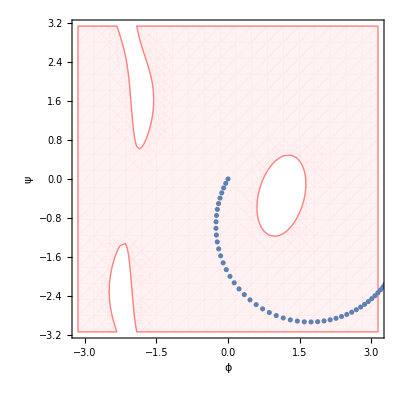

```mathematica
Show[DrawConfigRegion[{1, 3}, 1, rightfinger, Automatic, Red, {{-0.1, 0.1}, {-0.1, 0.1}}], ListPlot[opswitchConfigs[[All, 1;;2]]]]
```

```mathematica
Manipulate[Draw5bar[opswitchConfigs[[ii]], rightfinger, 0.1], {ii, 1, Length[opswitchConfigs], 1}]
```